```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/norbert/Dropbox (MIT)/StasPacking/Data/Johnson

```mathematica
FigDir="/Users/norbert/Dropbox (MIT)/StasPacking/figure_data/";
```

## Construct all possible subisomorphisms

Some color definitions:

```mathematica
cd=ColorData[3,"ColorList"]
```

{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237]}

```mathematica
myYellow=RGBColor[0.996078431372549, 0.8200000000000001, 0.03529411764705882];
colors={cd[[5]],myYellow,cd[[6]], Green, Blue, Purple};
(*colors={Gray,LightGray};*)
ngons=Union[Flatten[Map[First,PolyhedronData["Johnson","FaceCountRules"],{2}]]];
(*Vertex colors*)
MyLabelColors=Table[White,{i,1,16}];
MyLabelColors[[16]]=RGBColor[0.58,0.35,0.];
```

```mathematica
colors
```

{RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.996078431372549, 0.8200000000000001, 0.03529411764705882],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0.5, 0, 0.5]}

```mathematica
J90Plot=Graphics3D[Normal[PolyhedronData["Disphenocingulum","Faces", "Polygon"]]/.Polygon[x_]:>{EdgeForm[{AbsoluteThickness[10],Opacity[0.8]}],Specularity[0],Opacity[ 0.45],Lighter[colors[[Position[ngons,Length[x]][[1,1]]]]],Polygon[x]},Boxed->False,ViewPoint->{1.985765579012083,2.621257213134179,0.7973366213857535},ViewVertical->{-0.26056951097442915,1.06032043655769,-0.018426558909775813},Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
ABC=Normal[GeometricTransformation[{Normal[PolyhedronData["Disphenocingulum","Faces", "Polygon"]]/.Polygon[x_]:>{EdgeForm[{AbsoluteThickness[10],Opacity[0.8]}],Specularity[0],Opacity[ 0.45],Lighter[colors[[Position[ngons,Length[x]][[1,1]]]]],Polygon[x]}},ReflectionTransform[{0,0,1},{0,0,0}]]];
J90PlotMirrored=Graphics3D[ABC,Boxed->False,ViewPoint->{1.985765579012083,2.621257213134179,0.7973366213857535},ViewVertical->{-0.26056951097442915,1.06032043655769,-0.018426558909775813},Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
gr1={FaceForm[Red,Blue],Polygon[{{0,0,0},{1,0,0},{0,1,0}}]};
```

```mathematica
gr2={FaceForm[Red,Blue],Polygon[Reverse@{{0,0,0},{1,0,0},{0,1,0}}]};
```

```mathematica
ListPlot3D[RandomReal[1,{9,9}],InterpolationOrder->2,Mesh->None,PlotStyle->Specularity[50],Lighting->{{"Directional",RGBColor[1,.7,.1],{{5,5,4},{5,5,0}}}}]
```

```mathematica
{Graphics3D[gr2,PlotRange->{-.1,.1}, Lighting->"Neutral"],Graphics3D[Normal[GeometricTransformation[gr2,ReflectionMatrix[{0,0,1}]]],PlotRange->{-.1,.1},Lighting->"Neutral"],Graphics3D[tt,PlotRange->{-.1,.1}, Lighting->"Neutral"]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
tt=Normal[GeometricTransformation[gr2,ReflectionMatrix[{0,0,1}]]]
```

{FaceForm[RGBColor[1, 0, 0],RGBColor[0, 0, 1]],Polygon[{{0,0,0},{1,0,0},{0,1,0}},VertexNormals→Automatic,VertexColors→Automatic]}

```mathematica
gr2
```

{FaceForm[RGBColor[1, 0, 0],RGBColor[0, 0, 1]],Polygon[{{0,1,0},{1,0,0},{0,0,0}}]}

```mathematica
J90Plot=Graphics3D[Normal[PolyhedronData["Disphenocingulum","Faces", "Polygon"]]/.Polygon[x_]:>{EdgeForm[{AbsoluteThickness[10],Opacity[0.8]}],Specularity[0],Opacity[ 0.45],Lighter[colors[[Position[ngons,Length[x]][[1,1]]]]],Polygon[x]},Boxed->False,ViewPoint->{1.985765579012083,2.621257213134179,0.7973366213857535},ViewVertical->{-0.26056951097442915,1.06032043655769,-0.018426558909775813},Lighting->"Neutral"]
```

Import the RC tree and some visualization data (colors):

```mathematica
GD=Import["../GD_Mathematica.mat"]//First//First;
MyColors=Import["../MyColors_Mathematica.mat"]//First;
RCAdj=Round[Import["../eqSpheres/RCAdj.mat"][[1]]];
GRC=AdjacencyGraph[RCAdj];
RCa=GraphAutomorphismGroup[GRC];
NAutRC=GroupOrder[RCa];
RCDegrees = VertexDegree[GRC];
```

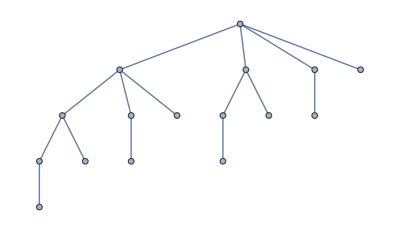

```mathematica
GRC
```

Obtain the J90 (Disphenocingulum) graph and Vertex coordinates.

```mathematica
DisphG=PolyhedronData["Disphenocingulum", "SkeletonGraph"];
DisphCoords = PolyhedronData["Disphenocingulum", "VertexCoordinates"];
```

```mathematica
GroupOrder[GraphAutomorphismGroup[DisphG]]
```

8

This is the IGraph package - only do this once:

```mathematica
PacletInstall["/Users/norbert/Downloads/IGraphM-0.3.90.paclet"]
```

Load the package:

```mathematica
<<IGraphM`
```

IGraph/M 0.3.90 (April 28, 2017)

Evaluate IGDocumentation[] to get started.

```mathematica
IGDocumentation[]
```

There are 5184 sub-isomorphisms with which the RC tree can be “embedded” within the Disphenocingulum:

```mathematica
IGVF2SubisomorphismCount[GRC,DisphG]
```

5184

Find all possibilities explicitly:

```mathematica
AllSubisos = IGVF2FindSubisomorphisms[GRC,DisphG];
```

```mathematica
AllCoords=Table[0,{i,1,Length[AllSubisos]}];
AllMaps=Table[0,{i,1,Length[AllSubisos]}];
(*AllInvMaps=Table[0,{i,1,Length[AllSubisos]}];*)
AllOrigCoords=Table[0,{i,1,Length[AllSubisos]}];
AllAdjs=Table[0,{i,1,Length[AllSubisos]}];
For[m=1,m≤Length[AllSubisos], m++,
map=AllSubisos[[m]];
inv=Apply[Normal,GroupBy[Normal[map],Last->First],1];
AllAdjs[[m]]=AdjacencyMatrix[DisphG][[Values[map],Values[map]]];
MappedCoords=DisphCoords[[Values[map]]];
Len=Sqrt[Total[MappedCoords^2,{2}]];
AllCoords[[m]]=MappedCoords/Len;
AllOrigCoords[[m]]=MappedCoords;
AllMaps[[m]]=Values[map];
(*AllInvMaps[[m]]=Keys[inv];*)
];
```

```mathematica
Export["J90SubisoCoords.mat",AllCoords];
Export["J90SubisoOrigCoords.mat",AllOrigCoords];
Export["J90SubisoAdjs.mat",AllAdjs];
Export["J90SubisoMaps.mat",AllMaps];
```

## Explicit construction of J90 graph states

Read back in the previously calculated adjacencies (from Mathematica) and corresponding tree states (from MATLAB):

```mathematica
AllCoords = Import["J90SubisoCoords.mat"];
AllOrigCoords = Import["J90SubisoOrigCoords.mat"];
AllAdjs = Import["J90SubisoAdjs.mat"];
AllStates=Round[Import["J90SubisoStates.mat"]][[1,1]];
AllMaps=Round[Import["J90SubisoMaps.mat"]][[1]];
```

This is the styling of the underlying graph into which we embed the tree:

```mathematica
tt=AdjacencyMatrix[DisphG];
GDisph=AdjacencyGraph[tt,GraphLayout->{"TutteEmbedding"},EdgeStyle->Directive[{AbsoluteThickness[3],Gray,Opacity[1]}],VertexSize->0.4];
```

```mathematica
vcoords=Values[First[AbsoluteOptions[GDisph,VertexCoordinates]]];
```

```mathematica
rmat=RotationTransform[Pi/4];
vcoordsnew=Map[rmat,vcoords];
vcoordsnew[[1]]={-0.3,0.5};
vcoordsnew[[4]]={-0.3,-0.5};
vcoordsnew[[5]]={0.6,0.5};
vcoordsnew[[8]]={-0.1,0};
vcoordsnew[[9]]={0.6,-0.5};
vcoordsnew[[10]]={0.35,0.27};
vcoordsnew[[15]]={0.35,-0.27};
vcoordsnew[[3]]={-0.2,0.22};
vcoordsnew[[6]]={-0.2,-0.22};
vcoordsnew[[7]]={0.1,0.21};
vcoordsnew[[13]]={0.1,-0.21};
vcoordsnew;
rmat=RotationTransform[Pi];
vcoordsnew=Map[rmat,vcoordsnew];
```

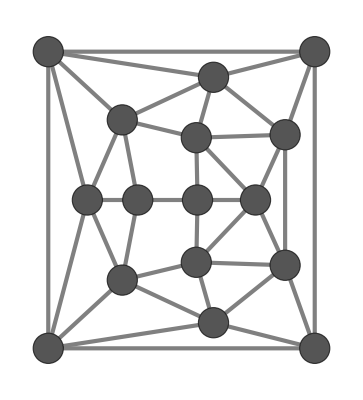

```mathematica
DisphGStyled=AdjacencyGraph[tt,GraphLayout->{"TutteEmbedding"},EdgeStyle->Directive[{AbsoluteThickness[3],Gray,Opacity[1]}],VertexSize->0.6,VertexCoordinates->vcoordsnew,VertexStyle->Darker[Gray]]
```

```mathematica
(*DisphGStyled=Graph[DisphG,EdgeStyle->Directive[{AbsoluteThickness[3],Gray,Opacity[1]}],VertexSize->0.4,GraphLayout->"CircularMultipartiteEmbedding"];*)
```

```mathematica
Tally[AllStates]
```

{{62,56},{26,80},{66,72},{30,88},{68,144},{32,152},{72,120},{36,144},{56,152},{60,136},{64,64},{28,104},{70,136},{34,152},{39,40},{45,72},{40,24},{46,80},{9,48},{15,72},{10,24},{16,72},{63,48},{27,80},{69,80},{33,112},{51,160},{58,216},{52,168},{3,144},{4,144},{22,144},{57,168},{61,32},{25,32},{65,40},{29,32},{67,88},{31,80},{71,72},{35,56},{55,104},{59,64},{1,80},{19,72},{24,48},{20,72},{54,80},{50,112},{21,80},{23,40},{5,24},{6,24},{2,72},{53,48},{49,80},{44,48},{14,48},{43,48},{13,48},{37,8},{47,8},{7,8},{17,8},{38,8},{48,8},{8,8},{18,8}}

Each embeddable tree state appears a multiple of 8 times, since there 8 automorphisms for J90:

```mathematica
GraphAutomorphismGroup[DisphG]//GroupOrder
```

8

## Analysis for state 13 (6 non-trivial embeddings)

We pick state 13 to plot all embeddings (6 possibilities up to trivial symmetries):

```mathematica
State1=13;
State1ID=Position[AllStates,State1]//Flatten;
FigStateDir=FigDir<>"AllJohnsonEmbeddings_State"<>ToString[State1];
CreateDirectory[FigStateDir];
```

CreateDirectory::filex: /Users/norbert/Dropbox (MIT)/StasPacking/figure_data/AllJohnsonEmbeddings_State13 already exists.

```mathematica
StateGraphs=Table[0,{i,1,Length[State1ID]/8}];
StatePlots=Table[0,{i,1,Length[State1ID]/8}];
keys=Table[i,{i,1,16}];
(*Fix position of first node to filter trivial symmetries of J90*)
PosV1=AllOrigCoords[[State1ID[[1+24]],1]];
ct=1;
For[s=1,s≤Length[State1ID],s++,
X1=AllOrigCoords[[State1ID[[s]]]];
If[X1[[1]]≠PosV1,Continue[]];
(*Construct permutation maps:*)
mapvals=AllMaps[[State1ID[[s]]]]; 
map=Table[keys[[i]]-> mapvals[[i]],{i,1,16}];inv=Apply[Normal,GroupBy[Normal[map],Last->First],1];
MyVertexLabels=Table[Keys[inv][[i]]-> Placed[Values[inv][[i]],{1.25,1.25}],{i,1,16}];
MyVertexStyles=Table[Keys[inv][[i]]-> Directive[35],{i,1,16}];
GM=Graph[VertexReplace[GRC,map]];
StateGraphs[[ct]]=Show[HighlightGraph[DisphGStyled,{Style[GM,{Darker[Red],AbsoluteThickness[7]}]},VertexLabels->MyVertexLabels,VertexLabelStyle->MyVertexStyles,VertexShapeFunction->Function[{pos,v,size}, Style[Disk[pos,size[[1]]],{EdgeForm[RGBColor[MyColors[[GD[[inv[v]]]+1]]]],RGBColor[MyColors[[GD[[inv[v]]]+1]]]}]]]];
(* Now the 3d plots of the embeddings:*)
CoordRule1=Table[i->X1[[i]],{i,1,16}];
StatePlots[[ct]]=Show[GraphPlot3D[GRC, VertexCoordinateRules->CoordRule1,
VertexRenderingFunction->({RGBColor[MyColors[[GD[[#2]]+1]]],Sphere[#1,0.17]}&),
EdgeRenderingFunction->({RGBColor[1,0.0,0.0],Cylinder[#1,.035]}&),
Lighting->"Neutral", Boxed->False],J90Plot ,ViewPoint->{1.985765579012083,2.621257213134179,0.7973366213857535},ViewVertical->{-0.26056951097442915,1.06032043655769,-0.018426558909775813}];
ct++;
];
```

Repeat the same with ALL isomorphisms (to fix the mirroring issues of above states 1 and 2):

```mathematica
StateGraphs=Table[0,{i,1,Length[State1ID]}];
StatePlots=Table[0,{i,1,Length[State1ID]}];
keys=Table[i,{i,1,16}];
(*Fix position of first node to filter trivial symmetries of J90*)
PosV1=AllOrigCoords[[State1ID[[1+24]],1]];
ct=1;
For[s=1,s≤Length[State1ID],s++,
X1=AllOrigCoords[[State1ID[[s]]]];
(*Construct permutation maps:*)
mapvals=AllMaps[[State1ID[[s]]]]; 
map=Table[keys[[i]]-> mapvals[[i]],{i,1,16}];inv=Apply[Normal,GroupBy[Normal[map],Last->First],1];
MyVertexLabels=Table[Keys[inv][[i]]-> Placed[Values[inv][[i]],{1.25,1.25}],{i,1,16}];
MyVertexStyles=Table[Keys[inv][[i]]-> Directive[35],{i,1,16}];
GM=Graph[VertexReplace[GRC,map]];
StateGraphs[[ct]]=Show[HighlightGraph[DisphGStyled,{Style[GM,{Darker[Red],AbsoluteThickness[7]}]},VertexLabels->MyVertexLabels,VertexLabelStyle->MyVertexStyles,VertexShapeFunction->Function[{pos,v,size}, Style[Disk[pos,size[[1]]],{EdgeForm[RGBColor[MyColors[[GD[[inv[v]]]+1]]]],RGBColor[MyColors[[GD[[inv[v]]]+1]]]}]]]];
(* Now the 3d plots of the embeddings:*)
CoordRule1=Table[i->X1[[i]],{i,1,16}];
StatePlots[[ct]]=Show[GraphPlot3D[GRC, VertexCoordinateRules->CoordRule1,
VertexRenderingFunction->({RGBColor[MyColors[[GD[[#2]]+1]]],Sphere[#1,0.17]}&),
EdgeRenderingFunction->({RGBColor[1,0.0,0.0],Cylinder[#1,.035]}&),
Lighting->"Neutral", Boxed->False],J90Plot ,ViewPoint->{1.985765579012083,2.621257213134179,0.7973366213857535},ViewVertical->{-0.26056951097442915,1.06032043655769,-0.018426558909775813}];
ct++;
];
```

The states that correspond to states 1 and 2 with correct orientation are s=8 (->state 1) and s=13 (->state 2). Use the routine below to mirror other states and find which one correspond to state 1 and state 2. Then we use the original, nonmirrored versions (i.e. mirrored version of state 1 and 2) for the paper.

```mathematica
s=13;
Trafo=ReflectionTransform[{0,0,1}];
X1=Trafo[AllOrigCoords[[State1ID[[s]]]]];
(*Construct permutation maps:*)
mapvals=AllMaps[[State1ID[[s]]]]; 
map=Table[keys[[i]]-> mapvals[[i]],{i,1,16}];inv=Apply[Normal,GroupBy[Normal[map],Last->First],1];
MyVertexLabels=Table[Keys[inv][[i]]-> Placed[Values[inv][[i]],{1.25,1.25}],{i,1,16}];
MyVertexStyles=Table[Keys[inv][[i]]-> Directive[35],{i,1,16}];
GM=Graph[VertexReplace[GRC,map]];
(* Now the 3d plots of the embeddings:*)
CoordRule1=Table[i->X1[[i]],{i,1,16}];
StatePlotsMirror=Show[GraphPlot3D[GRC, VertexCoordinateRules->CoordRule1,
VertexRenderingFunction->({RGBColor[MyColors[[GD[[#2]]+1]]],Sphere[#1,0.17]}&),
EdgeRenderingFunction->({RGBColor[1,0.0,0.0],Cylinder[#1,.035]}&),
Lighting->"Neutral", Boxed->False],J90PlotMirrored ,ViewPoint->{1.985765579012083,2.621257213134179,0.7973366213857535},ViewVertical->{-0.26056951097442915,1.06032043655769,-0.018426558909775813}];
```

```mathematica
Show[StatePlotsMirror,ViewPoint->{0.025241972077752875,0.49443479705260907,-3.347371666592937},ViewVertical->{-0.6857193448876152,0.538851444736108,-0.5938204904174776}]
```

-Graphics3D-

After identifying the correct states to replace state 1,2, we plot them in their original form:

```mathematica
StatePlots[[8]]
```

-Graphics3D-

```mathematica
StatePlots[[7]]
```

-Graphics3D-

```mathematica
For[p=1,p<=Length[StatePlots],p++,
Export[FigStateDir<>"/3DEmbedding_"<>ToString[p]<>".png",StatePlots[[p]],ImageResolution->200,Background->None];
];
```

```mathematica
For[p=1,p<=Length[StateGraphs],p++,
(*TR1 = Rasterize[StateGraphs[[p]], ImageResolution->300];*)
TR1=StateGraphs[[p]];
Export[FigStateDir<>"/GraphEmbedding_"<>ToString[p]<>".pdf",TR1,"AllowRasterization"->False];
];
```

Pretty plot of the general embedding problem:

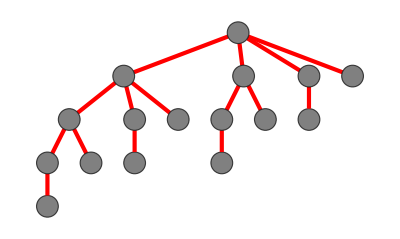

```mathematica
TreeG=Graph[GRC,VertexStyle->Gray,EdgeStyle->Directive[Opacity[1],AbsoluteThickness[3],Red],VertexSize->0.5]
```

```mathematica
Export[FigDir<>"RCTree.eps",TreeG];
```

```mathematica
State1ID=Position[AllStates,1]//Flatten;
mapvals=AllMaps[[State1ID[[1]]]]; 
map=Table[keys[[i]]-> mapvals[[i]],{i,1,16}];
GM=Graph[VertexReplace[GRC,map]];
DisphGStyledS=Graph[DisphGStyled,EdgeStyle->Directive[{Opacity[1],Lighter[Gray],AbsoluteThickness[9]}]];
Emb=HighlightGraph[DisphGStyledS,GM,VertexShapeFunction->Function[{pos,v,size}, Style[Disk[pos,size[[1]]],{EdgeForm[Black],Gray}]]];
```

```mathematica
Export[FigDir<>"J90ExampleEmbedding1.eps",Emb];
```

```mathematica
State1ID=Position[AllStates,1]//Flatten;
mapvals=AllMaps[[State1ID[[10]]]]; 
map=Table[keys[[i]]-> mapvals[[i]],{i,1,16}];
GM=Graph[VertexReplace[GRC,map]];
DisphGStyledS=Graph[DisphGStyled,EdgeStyle->Directive[{Opacity[1],Lighter[Gray],AbsoluteThickness[9]}]];
Emb=HighlightGraph[DisphGStyledS,GM,VertexShapeFunction->Function[{pos,v,size}, Style[Disk[pos,size[[1]]],{EdgeForm[Black],Gray}]]];
```

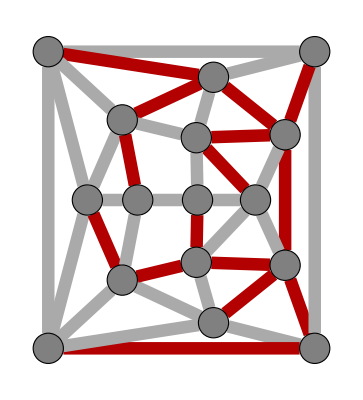

```mathematica
Emb
```

```mathematica
Export[FigDir<>"J90ExampleEmbedding2.eps",Emb];
```

```mathematica
X1=AllOrigCoords[[State1ID[[10]]]];
```

```mathematica
CoordRule1=Table[i->X1[[i]],{i,1,16}];pp=Show[GraphPlot3D[GRC, VertexCoordinateRules->CoordRule1,
VertexRenderingFunction->({RGBColor[MyColors[[GD[[#2]]+1]]],Sphere[#1,0.17]}&),
EdgeRenderingFunction->({RGBColor[1,0.0,0.0],Cylinder[#1,.035]}&),
Lighting->"Neutral", Boxed->False],J90Plot ,ViewPoint->{1.985765579012083,2.621257213134179,0.7973366213857535},ViewVertical->{-0.26056951097442915,1.06032043655769,-0.018426558909775813}];
```

```mathematica
Export[FigDir<>"J90Macrostate.png",pp,Background->None, ImageResolution->200];
```

## Analysis for state 48 (1 non-trivial embedding)

We pick state 48 to plot all embeddings (1 possibility up to trivial symmetries):

```mathematica
State1=48;
State1ID=Position[AllStates,State1]//Flatten;
FigStateDir=FigDir<>"AllJohnsonEmbeddings_State"<>ToString[State1];
CreateDirectory[FigStateDir];
```

CreateDirectory::filex: /Users/norbert/Dropbox (MIT)/StasPacking/figure_data/AllJohnsonEmbeddings_State48 already exists.

```mathematica
StateGraphs=Table[0,{i,1,Length[State1ID]/8}];
StatePlots=Table[0,{i,1,Length[State1ID]/8}];
keys=Table[i,{i,1,16}];
(*Fix position of first node to filter trivial symmetries of J90*)
PosV1=AllOrigCoords[[State1ID[[5]],1]];
ct=1;
For[s=1,s≤Length[State1ID],s++,
X1=AllOrigCoords[[State1ID[[s]]]];
If[X1[[1]]≠PosV1,Continue[]];
(*Construct permutation maps:*)
mapvals=AllMaps[[State1ID[[s]]]]; 
map=Table[keys[[i]]-> mapvals[[i]],{i,1,16}];inv=Apply[Normal,GroupBy[Normal[map],Last->First],1];
(*MyVertexLabels=Table[Keys[inv][[i]]-> Placed[Values[inv][[i]],{1/2,1/2}],{i,1,16}];
MyVertexStyles=Table[Keys[inv][[i]]-> Directive[17, MyLabelColors[[Values[inv][[i]]]]],{i,1,16}];*)
MyVertexLabels=Table[Keys[inv][[i]]-> Placed[Values[inv][[i]],{1.25,1.25}],{i,1,16}];
MyVertexStyles=Table[Keys[inv][[i]]-> Directive[35],{i,1,16}];
GM=Graph[VertexReplace[GRC,map]];
StateGraphs[[ct]]=Show[HighlightGraph[DisphGStyled,{Style[GM,{Darker[Red],AbsoluteThickness[7]}]},VertexLabels->MyVertexLabels,VertexLabelStyle->MyVertexStyles,VertexShapeFunction->Function[{pos,v,size}, Style[Disk[pos,size[[1]]],{EdgeForm[RGBColor[MyColors[[GD[[inv[v]]]+1]]]],RGBColor[MyColors[[GD[[inv[v]]]+1]]]}]]]];
(* Now the 3d plots of the embeddings:*)
CoordRule1=Table[i->X1[[i]],{i,1,16}];
StatePlots[[ct]]=Show[GraphPlot3D[GRC, VertexCoordinateRules->CoordRule1,
VertexRenderingFunction->({RGBColor[MyColors[[GD[[#2]]+1]]],Sphere[#1,0.17]}&),
EdgeRenderingFunction->({RGBColor[1,0.0,0.0],Cylinder[#1,.035]}&),
Lighting->"Neutral", Boxed->False],J90Plot ,ViewPoint->{1.985765579012083,2.621257213134179,0.7973366213857535},ViewVertical->{-0.26056951097442915,1.06032043655769,-0.018426558909775813}];
ct++;
];
```

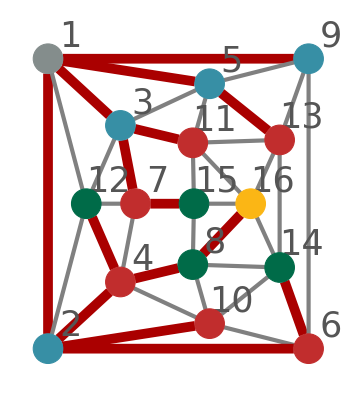

```mathematica
StateGraphs[[1]]
```

```mathematica
For[p=1,p<=Length[StatePlots],p++,
Export[FigStateDir<>"/3DEmbedding_"<>ToString[p]<>".png",StatePlots[[p]],ImageResolution->200,Background->None];
];
```

```mathematica
For[p=1,p<=Length[StateGraphs],p++,
(*TR1 = Rasterize[StateGraphs[[p]], ImageResolution->300];*)
TR1=StateGraphs[[p]];
Export[FigStateDir<>"/GraphEmbedding_"<>ToString[p]<>".pdf",TR1, "AllowRasterization"->False];
];
```

## Debugging routines down here:

```mathematica
VertexReplace[GRC,Normal[map]]
```

```mathematica
DisphRL=VertexReplace[DisphG,Normal[inv]]
```

```mathematica
AdjacencyMatrix[DisphG]//MatrixForm
```

```mathematica
adjnew=AdjacencyMatrix[DisphG][[Values[map],Values[map]]];
```

```mathematica
adjnew//MatrixForm
```

```mathematica
DisphCoords//MatrixForm
```

```mathematica
tt=Sqrt[Total[DisphCoords[[Values[map]]]^2,{2}]]
```

{1.21235,1.02606,1.02606,1.02607,1.21235,1.17243,1.02606,1.02606,1.17243,1.02606,1.17243,1.17243,1.02607,1.21234,1.21234,1.02606}

```mathematica
nn=DisphCoords[[Values[map]]]/tt
```

{{-0.966016,0.242248,0.0901654},{-0.79375,-0.523888,-0.309034},{-0.448744,0.449363,0.772465},{-0.302008,0.0175463,-0.953144},{-0.54983,0.700488,-0.454976},{0.0089408,-0.768803,-0.639424},{0.110579,-0.331633,0.936905},{0.640175,-0.135276,-0.756225},{-0.715414,-0.390344,0.579496},{-0.114288,-0.965977,0.232006},{0.452313,0.481939,0.750431},{0.25416,0.677206,-0.690503},{0.0429986,0.990796,0.128354},{0.662764,-0.739807,-0.115887},{0.853079,-0.202931,0.480703},{0.865042,0.499068,-0.0513268}}

```mathematica
Sqrt[Total[nn^2,{2}]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
DisphCoords[[Values[map]]]//MatrixForm
```

(-1.17114 | 0.293688 | 0.109312
-0.814439 | -0.537542 | -0.317089
-0.46044 | 0.461075 | 0.792599
-0.30988 | 0.0180037 | -0.977988
-0.666585 | 0.849234 | -0.551588
0.0104825 | -0.901367 | -0.749679
0.113461 | -0.340277 | 0.961325
0.656861 | -0.138802 | -0.775936
-0.83877 | -0.457649 | 0.679417
-0.117267 | -0.991154 | 0.238053
0.530305 | 0.56504 | 0.879827
0.297985 | 0.793976 | -0.809566
0.0441194 | 1.01662 | 0.131699
0.803499 | -0.896901 | -0.140495
1.03423 | -0.246023 | 0.582777
0.887588 | 0.512075 | -0.0526646)

```mathematica
CoordRule
```

{1→{-1.17114,0.293688,0.109312},2→{-0.814439,-0.537542,-0.317089},3→{-0.46044,0.461075,0.792599},4→{-0.30988,0.0180037,-0.977988},5→{-0.666585,0.849234,-0.551588},6→{0.0104825,-0.901367,-0.749679},7→{0.113461,-0.340277,0.961325},8→{0.656861,-0.138802,-0.775936},9→{-0.83877,-0.457649,0.679417},10→{-0.117267,-0.991154,0.238053},11→{0.530305,0.56504,0.879827},12→{0.297985,0.793976,-0.809566},13→{0.0441194,1.01662,0.131699},14→{0.803499,-0.896901,-0.140495},15→{1.03423,-0.246023,0.582777},16→{0.887588,0.512075,-0.0526646}}

```mathematica
NewG=AdjacencyGraph[adjnew];
CoordRule=Table[i->DisphCoords[[map[i]]],{i,1,16}];
```

```mathematica
CoordRule=Table[i->nn[[i]],{i,1,16}];
```

```mathematica
GraphPlot3D[NewG,VertexCoordinateRules->CoordRule,VertexLabeling->True,VertexRenderingFunction->({RGBColor[MyColors[[GD[[#2]]+1]]],Sphere[#1,.2]}&),Lighting->"Neutral"]
```

-Graphics3D-

-Graphics3D-

```mathematica
GraphPlot3D[DisphG,VertexCoordinateRules-> CoordRule, VertexLabeling->All, VertexRenderingFunction->(Sphere[#1,.2]&)]
```

-Graphics3D-

```mathematica
GraphPlot3D[DisphRL,VertexLabeling->True]
```

-Graphics3D-

```mathematica
DisphG
```

Test embeddings into original graph:

```mathematica
State1ID[[1+24]]
```

2634

```mathematica
mapvals=AllMaps[[State1ID[[1]]]];
keys=Table[i,{i,1,16}];
map=Table[keys[[i]]-> mapvals[[i]],{i,1,16}];
inv=Apply[Normal,GroupBy[Normal[map],Last->First],1];
```

```mathematica
MyVertexLabels=Table[Keys[inv][[i]]-> Placed[Values[inv][[i]],{1/2,1/2}],{i,1,16}];
MyVertexStyles=Table[Keys[inv][[i]]-> Directive[13, MyLabelColors[[Values[inv][[i]]]]],{i,1,16}]
```

{3→Directive[13,GrayLevel[1]],6→Directive[13,GrayLevel[1]],1→Directive[13,GrayLevel[1]],11→Directive[13,GrayLevel[1]],7→Directive[13,GrayLevel[1]],13→Directive[13,GrayLevel[1]],5→Directive[13,GrayLevel[1]],15→Directive[13,GrayLevel[1]],2→Directive[13,GrayLevel[1]],8→Directive[13,GrayLevel[1]],4→Directive[13,GrayLevel[1]],9→Directive[13,GrayLevel[1]],10→Directive[13,GrayLevel[1]],14→Directive[13,GrayLevel[1]],12→Directive[13,GrayLevel[1]],16→Directive[13,RGBColor[0.58, 0.35, 0.]]}

```mathematica
GM=Graph[VertexReplace[GRC,map]];
```

```mathematica
t=HighlightGraph[DisphGStyled,GM,VertexLabels->MyVertexLabels,VertexLabelStyle->MyVertexStyles,VertexShapeFunction->Function[{pos,v,s}, Style[Disk[pos,s[[1]]],{EdgeForm[RGBColor[MyColors[[GD[[inv[v]]]+1]]]],RGBColor[MyColors[[GD[[inv[v]]]+1]]]}]]]
```

```mathematica
GRC
```

```mathematica
Rasterize[t,ImageResolution->200]
```

-Graphics-